# -Graphics-

# Scientific Computing with Mathematica

## Part (1): linear Algebra

-Graphics-

## Outline

### Matrices

Entering and Displaying Matrices

Assembling Matrices Quickly with the Table Command

Creating Special Matrices

Concatenating Matrices

Extracting Parts of Matrices

### Operations on Matrices

Adding and Subtracting Matrices

Matrix Multiplication

Matrix Power, Exponential, Transpose, Trace, Determinant and Inverse

### Sparse Linear Algebra

Creating Sparse Arrays

Creating Banded Sparse Matrices

### Solving Linear Systems

The LinearSolve Function

Direct and Iterative Methods

Null Space and Rank of a Linear System

### Eigensystems

### Matrix Factorizations

The QR Decomposition

The Singular Value Decomposition

Other Matrix Decompositions

## Matrices

### Entering Matrices

To enter a matrix in Mathematica®, type a name for your matrix followed by an equal sign. Then from the menu bar select Insert ▶ Table/Matrix ▶ New.

Select Matrix and input the matrix dimensions, then click OK.

Fill the placeholders and use the tab key to move to the next matrix entry:

```mathematica
ℳ = ({{1, 2, 3}, {5, 8, 9}, {0, 5, 7}})
```

{{1,2,3},{5,8,9},{0,5,7}}

Mathematica thinks of a matrix as a list of lists. Each row is enclosed in curly brackets with entries separated by commas, the rows are separated by commas, and the entire matrix is enclosed in curly brackets.

You can enter a matrix in this form but it can be a little messy:

```mathematica
𝒩 = {{1,2,3},{5,8,9},{0,5,7}}
```

{{1,2,3},{5,8,9},{0,5,7}}

A third way to enter a matrix is by using the Basic Math Assistant palette.

Avoid using single-letter symbols such as C, D, E, I, K and N when naming a matrix, as these letters already have a designated purpose.  
If you insist on using these letters for naming matrices, you can use their scripted or Greek versions.

## Matrices

### Displaying Matrices

You can use the MatrixForm function whenever you want a nice look at your matrix:

```mathematica
A = {{0,1} , {5,6}}; 
MatrixForm[A]
```

(0 | 1
5 | 6)

### Matrix Dimensions

The Dimensions command returns a list containing the number of rows and columns in the matrix, respectively:

```mathematica
Dimensions[A]
```

{2,2}

## Matrices

### Creating Matrices Quickly

There are several commands that produce matrices quickly:

To get a 3×5 matrix with random integers between 0 and 10:

```mathematica
RandomInteger[10,{3,5}]//MatrixForm
```

(10 | 2 | 6 | 10 | 9
6 | 1 | 2 | 7 | 8
9 | 5 | 8 | 7 | 4)

The Table command can be used to enter matrices. The next command gives a 5×5 matrix whose i, j^th entry is  i+j:

```mathematica
Table[i+j,{i,5},{j,5}]//MatrixForm
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10)

The iterators can be set to start at values other than 1:

```mathematica
Table[i+ j,{i,-2,3},{j,0,2}]//MatrixForm
```

(-2 | -1 | 0
-1 | 0 | 1
0 | 1 | 2
1 | 2 | 3
2 | 3 | 4
3 | 4 | 5)

To get a 3×4 zero matrix, you can type this:

```mathematica
Table[0,{3},{4}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Or use the ConstantArray command:

```mathematica
ConstantArray[0 , {3,4}] //MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

You can produce a 4×4 lower triangular matrix with entries on and below the diagonal equal to i+j:

```mathematica
Table[If[i≥j,i+j,0],{i,4},{j,4}]//MatrixForm
```

(2 | 0 | 0 | 0
3 | 4 | 0 | 0
4 | 5 | 6 | 0
5 | 6 | 7 | 8)

## Matrices

### Special Matrices

The following command returns an identity matrix of the specified size:

```mathematica
IdentityMatrix[5]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

The following command gives a diagonal matrix with the enclosed list on the diagonal:

```mathematica
DiagonalMatrix[{1,2,3}]//MatrixForm
```

(1 | 0 | 0
0 | 2 | 0
0 | 0 | 3)

You can also use DiagonalMatrix to create a superdiagonal matrix:

```mathematica
DiagonalMatrix[{1,2,3},1]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 3
0 | 0 | 0 | 0)

The second difference matrix could be created as follows:

```mathematica
n = 5; 
DiagonalMatrix[Table[-2,{n}]] + DiagonalMatrix[Table[1,{n-1}],1] + DiagonalMatrix[Table[1,{n-1}],-1]   //MatrixForm
```

(-2 | 1 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0
0 | 1 | -2 | 1 | 0
0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 1 | -2)

## Matrices

### Concatenating Matrices

A handy way to build a new matrix from existing matrices is with the command ArrayFlatten:

```mathematica
A = RandomInteger[5, {3,4}];
A //MatrixForm
```

(0 | 5 | 1 | 3
0 | 0 | 0 | 0
5 | 2 | 4 | 1)

```mathematica
B = RandomInteger[5, {3,4}];
B //MatrixForm
```

(0 | 4 | 5 | 0
0 | 3 | 5 | 4
3 | 2 | 0 | 3)

To concatenate A and B matrices vertically:

```mathematica
ArrayFlatten[{{A},{B}}] // MatrixForm
```

(3 | 2 | 0 | 0
2 | 4 | 1 | 5
5 | 2 | 1 | 2
0 | 4 | 5 | 0
0 | 3 | 5 | 4
3 | 2 | 0 | 3)

To concatenate A and B matrices horizontally:

```mathematica
ArrayFlatten[{{A,B}}] // MatrixForm
```

(3 | 2 | 0 | 0 | 0 | 4 | 5 | 0
2 | 4 | 1 | 5 | 0 | 3 | 5 | 4
5 | 2 | 1 | 2 | 3 | 2 | 0 | 3)

You can also form a block matrix:

```mathematica
ArrayFlatten[{{A , 0 , 0},{0,B, 0},{A, B,0}}] // MatrixForm
```

(10 | 21 | 3 | 0 | 0 | 0 | 0 | 0
4 | 5 | 6 | 0 | 0 | 0 | 0 | 0
25 | 85 | 7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 5 | 0 | 0
0 | 0 | 0 | 0 | 3 | 5 | 4 | 0
0 | 0 | 0 | 3 | 2 | 0 | 3 | 0
10 | 21 | 3 | 0 | 4 | 5 | 0 | 0
4 | 5 | 6 | 0 | 3 | 5 | 4 | 0
25 | 85 | 7 | 3 | 2 | 0 | 3 | 0)

## Matrices

### Extracting Parts of Matrices

Always remember that internally Mathematica thinks of a matrix as a list of lists:

```mathematica
A = {{10,21,3},{4,5,6},{25,85,7}};
A//MatrixForm
```

(10 | 21 | 3
4 | 5 | 6
25 | 85 | 7)

The basic rule is that you use double square brackets to refer to individual items in a list:

```mathematica
A [[1]]
```

{10,21,3}

To retrieve the entry in row 3, column 2, type:

```mathematica
A[[3,2]]
```

85

To extract a single column, indicate that you want All rows. For example, to get the second column, type:

```mathematica
A[[All,2]]
```

{21,5,85}

Use Span, whose infix form is ;;, to specify a span of rows and/or columns.Here, take the first
through second columns:

```mathematica
A[[All,1;;2]]//MatrixForm
```

(10 | 21
4 | 5
25 | 85)

## Matrix Operations

### Adding and Subtracting Matrices

A = (0 | 8 | 2
2 | 5 | 1
3 | 4 | 3);   B= (1 | 8 | 2
3 | 9 | 1
7 | 8 | 2);

The + and - operators work as expected for matrices:

```mathematica
A+B //MatrixForm
```

(1 | 16 | 4
5 | 14 | 2
10 | 48 | 5)

```mathematica
A-B //MatrixForm
```

(-1 | 0 | 0
-1 | -4 | 0
-4 | -4 | 1)

You can also perform scalar multiplication:

```mathematica
5 *A //MatrixForm
```

(0 | 40 | 10
10 | 25 | 5
15 | 20 | 15)

## Matrix Operations

### Multiplying Matrices

A = (0 | 8 | 2
2 | 5 | 1
3 | 4 | 3);   B= (1 | 8 | 2
3 | 9 | 1
7 | 8 | 2);

In Mathematica, use the dot to take the product of matrices:

```mathematica
A. B //MatrixForm
```

(38 | 88 | 12
24 | 69 | 11
36 | 84 | 16)

Be careful to use the dot to perform matrix multiplication. The symbol * will do elementwise multiplication.

```mathematica
A * B //MatrixForm
```

(0 | 64 | 4
6 | 45 | 1
21 | 32 | 6)

## Matrix Operations

### Matrix Transpose

```mathematica
A = ({{0, 8.0, 2}, {2, 5, 1}, {3, 4, 3}});
```

The Transpose command will produce the transpose of a matrix:

```mathematica
Transpose[A]//MatrixForm
```

(0 | 2 | 3
8. | 5 | 4
2 | 1 | 3)

### Matrix Adjoint

```mathematica
ConjugateTranspose[A]//MatrixForm
```

(0 | 2 | 3
8. | 5 | 4
2 | 1 | 3)

## Matrix Operations

### Matrix Power

To find a power of a matrix, use the command MatrixPower:

```mathematica
MatrixPower[A,3] //MatrixForm
```

(138. | 472. | 134.
126. | 377. | 107.
169. | 492. | 147.)

### Matrix Exponential

To find a power of a matrix, use the command MatrixExp:

```mathematica
MatrixExp[A] //MatrixForm
```

(1424.56 | 4362.36 | 1251.52
1171.05 | 3587.79 | 1028.08
1555.42 | 4756.01 | 1370.71)

## Matrix Operations

### Matrix Inverse

For a nonsingular matrix M, the Inverse command will output its inverse:

```mathematica
M = RandomReal[5,{5,5}];
M  . Inverse[M];
Round[%] //MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

### Matrix Determinant

To find the determinant of a matrix, use the command Det:

```mathematica
Det[M] //MatrixForm
```

-133.26

### Matrix Trace

To find the trace of a matrix, use the command Tr:

```mathematica
Tr[M] //MatrixForm
```

12.0119

## Sparse Linear Algebra

In many applications in scientific computing (especially, numerical PDEs), arrays that arise are sparse (almost all of the entries are zero), 
so it is computationally efficient to store only the nonzero entries and their positions:

```mathematica
s=SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3,{1,3}->4}]
s //MatrixForm
```

SparseArray[…]

(1 | 0 | 4
0 | 2 | 0
0 | 0 | 3)

Equivalently, you can enter a list of positions and a list of corresponding values:

```mathematica
SparseArray[{{1,1},{2,2},{3,3},{1,3}}-> {1,2,3,4}] //MatrixForm
```

(1 | 0 | 4
0 | 2 | 0
0 | 0 | 3)

You can create a band diagonal matrix with the help of the Band command:

```mathematica
SparseArray[{Band[{1,1}]->1,Band[{2,1}]->-1},{5,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0
0 | 0 | -1 | 1 | 0
0 | 0 | 0 | -1 | 1)

MatrixPlot can be used to visualize the sparsity pattern of large sparse matrices:

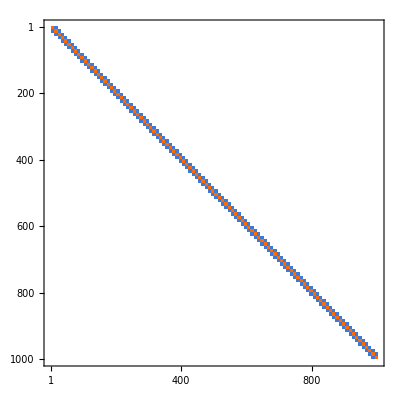

```mathematica
SparseArray[{Band[{1,1}]->2,Band[{2,1}]->-1,Band[{1,2}]->-1},{1000,1000}] //MatrixPlot
```

## Solving Linear Systems of Equations

The command LinearSolve provides a quick means for solving systems that have a single solution:

```mathematica
A = SparseArray[{Band[{1,1}]->2,Band[{2,1}]->-1,Band[{1,2}]->-1},{1000,1000}] ; 
b = ConstantArray[1.0, 1000];
x = LinearSolve[A,b] ;
```

As is typical with Mathematica, the solution method is chosen automatically for you.

With the Method option, you can choose different direct or iterative solution algorithms appropriate for the matrix structure (symmetric, positive definite, nonsymmetric, …)

The Cholesky method is suitable for solving symmetric positive definite systems:

```mathematica
Timing[LinearSolve[A,b,Method->"Cholesky"];]
```

{0.006165,Null}

The default method for Krylov iterative methods, BiCGSTAB, is more expensive but more generally applicable for nonsymmetric matrices:

```mathematica
Timing[LinearSolve[A,b,Method->"Krylov"];]
```

{0.000942,Null}

## Solving Linear Systems of Equations

### Null Space and Rank

Find the null space of a 3×3 matrix:

```mathematica
m = {{1,2,3},{4,5,6},{7,8,9}};
NullSpace[m]
```

{{1,-2,1}}

The action of m on the vector is the zero vector:

```mathematica
m . {1,-2,1}
```

{0,0,0}

Find the number of linearly independent rows:

```mathematica
MatrixRank[m]
```

2

```mathematica
Length[NullSpace[m]] + MatrixRank[m] == Dimensions[m][[1]]
```

True

## Eigenvalues and Eigenvectors

If you give a matrix of approximate real numbers, the Wolfram Language™ will find the approximate numerical eigenvalues and eigenvectors:

```mathematica
m={{2.3,4.5},{6.7,-1.2}}
```

{{2.3,4.5},{6.7,-1.2}}

The matrix has two eigenvalues, in this case both real:

```mathematica
Eigenvalues[m]
```

{6.31303,-5.21303}

Here are the two eigenvectors of m:

```mathematica
Eigenvectors[m]
```

{{0.746335,0.66557},{-0.513839,0.857886}}

Eigensystem computes the eigenvalues and eigenvectors at the same time. The assignment sets vals to the list of eigenvalues and vecs to the list of eigenvectors:

```mathematica
{vals,vecs}=Eigensystem[m]
```

{{6.31303,-5.21303},{{0.746335,0.66557},{-0.513839,0.857886}}}

## Matrix Decompositions

## The QR Decomposition

The QR decomposition of a matrix is a factorization of a full rank matrix into a product of an orthonormal matrix Q and a matrix R that is invertible and upper triangular.

The command QRDecomposition is used to compute the QR decomposition:

```mathematica
{Q, R} = QRDecomposition[{{1.,2.,3.},{4.,5.,6.}}]
```

{{{-0.242536,-0.970143},{-0.970143,0.242536}},{{-4.12311,-5.33578,-6.54846},{0.,-0.727607,-1.45521}}}

```mathematica
Q . R
```

{{1.,2.,3.},{4.,5.,6.}}

## Matrix Decompositions

## The Singular Value Decomposition SVD A=U W Transpose[V]

The singular value decomposition has many applications in data analysis and is a key algorithm in machine learning.

SVD reveals a great deal of useful information about norms, rank and subspaces.

Consider a singular 3×3 matrix m:

```mathematica
m=N[{{1,2,3},{4,5,6},{7,8,9}}];
```

Find the full singular value decomposition of m:

```mathematica
{u,w,v}=SingularValueDecomposition[m]
```

{{{-0.214837,-0.887231,0.408248},{-0.520587,-0.249644,-0.816497},{-0.826338,0.387943,0.408248}},{{16.8481,0.,0.},{0.,1.06837,0.},{0.,0.,0.}},{{-0.479671,0.776691,0.408248},{-0.572368,0.0756865,-0.816497},{-0.665064,-0.625318,0.408248}}}

The original matrix can be reconstructed from the singular value decomposition:

```mathematica
u.w.Transpose[v]
```

{{1.,2.,3.},{4.,5.,6.},{7.,8.,9.}}

## Matrix Decompositions

## Other Matrix Decompositions

```mathematica
?LUDecomposition
```

```mathematica
?SchurDecomposition
```

```mathematica
?JordanDecomposition
```

## References

Linear Algebra

Sparse Linear Algebra